## Vector addition and vector (and scalar) sign figures: VectorsWithOppositeOrientationFig1.eps, vectorAdditionFig1.eps, scalarOrientationFig1.eps

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

\\wsl$\Ubuntu\home\pjoot\project\figures\GAelectrodynamics

```mathematica
(*<<MaTeX`*)

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
ClearAll[bold, fs]

bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;
```

```mathematica
ClearAll[e1,e2, o]

(*{e1,e2,e3}= IdentityMatrix[3];*)
{e1,e2}= IdentityMatrix[2];
o = {0,0};

ClearAll[clk, ctr, rp, rn]
ctr =RotationTransform[Pi/2];
clk =RotationTransform[-Pi/2];
rp = ctr[#//Normalize] &;
rn = clk[#//Normalize] &;
```

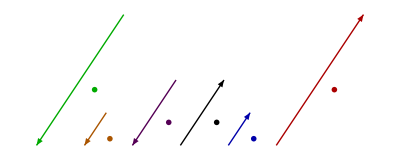

```mathematica
ClearAll[mmx2, mmxh, mmx, mx, mxh, mx2]

(*mmx2 = Row[{"-2"//fs, "x"//bold//fs}];
mmxh = Row[{"-"//fs,"x"//bold//fs}]/("2" //fs);
mmx = Row[{"-"//fs,"x"//bold//fs}];
mx = "x"//bold//fs;
mxh = ("x"//bold//fs)/("2" //fs);
mx2 = Row[{"2"//fs,"x"//bold//fs}];
*)

mmx2 = MaTeX["{\\color{GreenDarker}-2 \\mathbf{x}}"];
mmxh = MaTeX["{\\color{OrangeDarker}- \\frac{1}{2} \\mathbf{x}}"];
mmx = MaTeX["{\\color{PurpleDarker}-  \\mathbf{x}}"];
mx = MaTeX["{\\color{PurpleDarker} \\mathbf{x}}"];
mxh = MaTeX["{\\color{BlueDarker} \\frac{1}{2} \\mathbf{x}}"];
mx2 = MaTeX["{\\color{RedDarker} 2 \\mathbf{x}}"];


ClearAll[pscaling]
pscaling=Module[{x0,x1,h0,h1,d0,d1,n0,n1,nh0,nh1,hd0,nd1, s, of},
x0=o;
of= 0.8;
s = 2.2 e1;
x1=2(e1+1.5 e2);
(*half*)
h0=x0+s;
h1=x1/2+s;
(*double*)
d0=x0+2 s;
d1=2 x1+2 s;
(*negated*)
n0=x1-s;
n1=x0-s;
(*half negated*)
nh0=x1/2-2 s;
nh1=x0-2 s;
(*double negated*)
nd0=2 x1-3 s;
nd1=x0-3 s;
Graphics[{
Thick,
Arrowheads[0.05],

Green//Darker,Arrow[{nd0,nd1}],
Text[mmx2,(nd0+nd1)/2+of rp[nd1-nd0]],
Orange//Darker,Arrow[{nh0,nh1}],
Text[mmxh,(nh0+nh1)/2+of rp[nh1-nh0]], 
Purple//Darker,Arrow[{n0,n1}],
Text[mmx,(n0+n1)/2+of rp[n1-n0]], 
Black,Arrow[{x0,x1}],
Text[mx,(x0+x1)/2-of rp[x1-x0]],
Blue//Darker,Arrow[{h0,h1}],
Text[mxh,(h0+h1)/2-of rp[h1-h0]],
Red//Darker,Arrow[{d0,d1}],
Text[mx2,(d0+d1)/2-of rp[d1-d0]]
}]]
```

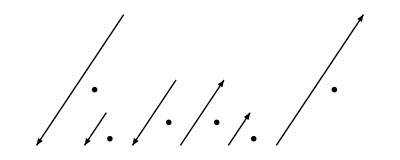

```mathematica
ClearAll[mmx2, mmxh, mmx, mx, mxh, mx2]


mmx2 = MaTeX["-2 \\mathbf{x}"];
mmxh = MaTeX["-\\frac{1}{2} \\mathbf{x}"];
mmx = MaTeX["-\\mathbf{x}"];
mx = MaTeX["\\mathbf{x}"];
mxh = MaTeX["\\frac{1}{2} \\mathbf{x}"];
mx2 = MaTeX["2 \\mathbf{x}"];


ClearAll[pscalingbw]
pscalingbw=Module[{x0,x1,h0,h1,d0,d1,n0,n1,nh0,nh1,hd0,nd1, s, of},
x0=o;
of= 0.8;
s = 2.2 e1;
x1=2(e1+1.5 e2);
(*half*)
h0=x0+s;
h1=x1/2+s;
(*double*)
d0=x0+2 s;
d1=2 x1+2 s;
(*negated*)
n0=x1-s;
n1=x0-s;
(*half negated*)
nh0=x1/2-2 s;
nh1=x0-2 s;
(*double negated*)
nd0=2 x1-3 s;
nd1=x0-3 s;
Graphics[{
Thick,
Arrowheads[0.05],

Arrow[{nd0,nd1}],
Text[mmx2,(nd0+nd1)/2+of rp[nd1-nd0]],
Arrow[{nh0,nh1}],
Text[mmxh,(nh0+nh1)/2+of rp[nh1-nh0]], 
Arrow[{n0,n1}],
Text[mmx,(n0+n1)/2+of rp[n1-n0]], 
Arrow[{x0,x1}],
Text[mx,(x0+x1)/2-of rp[x1-x0]],
Arrow[{h0,h1}],
Text[mxh,(h0+h1)/2-of rp[h1-h0]],
Arrow[{d0,d1}],
Text[mx2,(d0+d1)/2-of rp[d1-d0]]
}]]
```

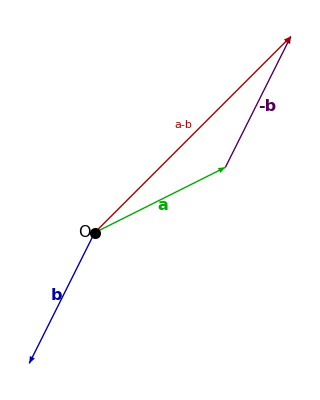

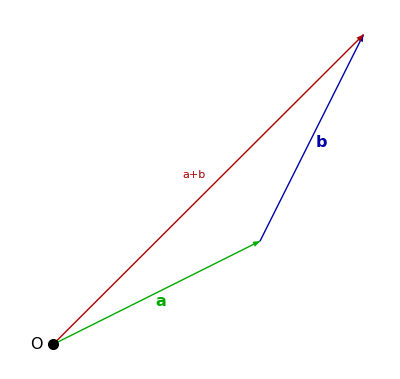

```mathematica
ClearAll[pdiffoftwo]
pdiffoftwo = Module[{a,b,mb,vd,vs},
a = e1 + 0.5e2;
b = -(0.5 e1 + e2);
mb = -b;
vs = a + b;
vd = a - b;

Graphics[ {
Thick,
Arrowheads[0.05],

Green // Darker,
Arrow[{o,a}],
Text["a"//bold//fs, a/2+0.05 rn[a] ],

Blue // Darker,
Arrow[{o,o + b} ],
Text["b"//bold//fs, o + b/2+0.05 rn[b]],

Purple // Darker,
Arrow[{a,a +(-b)} ],
Text["-b"//bold//fs, a - b/2+0.08 rn[-b]],

Red // Darker,
Arrow[{o,vd} ],
Text[Row[{
"a"//bold//fs,
"-" // fs,
"b"//bold//fs}]
, vd/2 + 0.1rp[vd]],

Black,
PointSize[0.02],
Point[o],
Text["O" // fs, {-0.08,0}]
}]
]

ClearAll[psumoftwo]
psumoftwo = Module[{a,b,vs},
a = e1 + 0.5e2;
b = (0.5 e1 + e2);

vs = a + b;


Graphics[ {
Thick,
Arrowheads[0.05],

Green // Darker,
Arrow[{o,a}],
Text["a"//bold//fs, a/2+0.05 rn[a] ],

Blue // Darker,
Arrow[{a,a + b} ],
Text["b"//bold//fs, a + b/2+0.05 rn[b]],

Red // Darker,
Arrow[{o,vs} ],
Text[Row[{
"a"//bold//fs,
"+" // fs,
"b"//bold//fs}]
, vs/2 + 0.1rp[vs]],

Black,
PointSize[0.02],
Point[o],
Text["O" // fs, {-0.08,0}]
}]
]
```

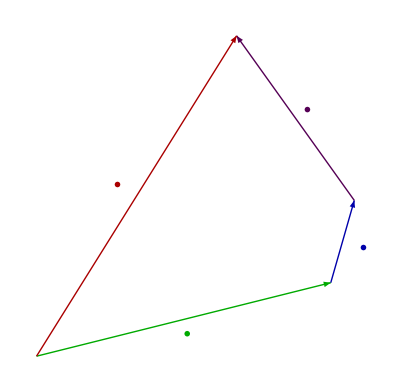

```mathematica
ClearAll[psumofthree]
psumofthree = Module[{v1,v2,v3,v12, v23, v13},
v1 = (0.5)(e1 + 0.25e2);
v2 = (0.2)(0.2 e1 + 0.7e2);
v3 = (0.4)(-0.5 e1 + 0.7 e2);
v12 = v1 + v2 ;
v13 = v1 + v2 + v3;

Graphics[ {
Thick
,Arrowheads[0.05]

, Green // Darker
,Arrow[{o,v1}]
(*,Text["a"//bold//fs, v1/2+0.05 rn[v1] ]*)
,Text[MaTeX["{\\color{GreenDarker}\\mathbf{a}}"], v1/2+0.025 rn[v1] ]

,Blue // Darker
,Arrow[{v1,v12} ]
(*,Text["b"//bold//fs, v1 + v2/2+0.07 rn[v2]]*)
,Text[MaTeX["{\\color{BlueDarker}\\mathbf{b}}"], v1 + v2/2+0.037 rn[v2]]

,Purple // Darker
,Arrow[{v12,v13} ]
(*,Text["c"//bold//fs, v12 + v3/2+0.05 rn[v3]]*)
,Text[MaTeX["{\\color{PurpleDarker}\\mathbf{c}}"], v12 + v3/2+0.025 rn[v3]]

,Red // Darker
,Arrow[{o,v13} ]

,Text[MaTeX["{\\color{RedDarker}\\mathbf{s}}"], v13/2 + 0.04rp[v13]]

}]
]
```

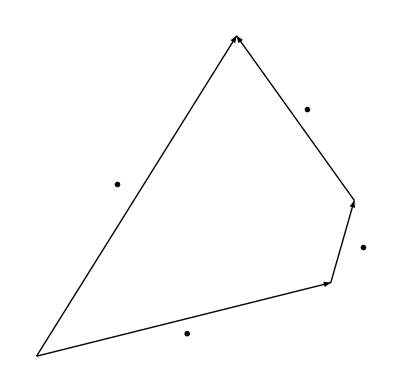

```mathematica
ClearAll[psumofthreebw]
psumofthreebw = Module[{v1,v2,v3,v12, v23, v13},
v1 = (0.5)(e1 + 0.25e2);
v2 = (0.2)(0.2 e1 + 0.7e2);
v3 = (0.4)(-0.5 e1 + 0.7 e2);
v12 = v1 + v2 ;
v13 = v1 + v2 + v3;

Graphics[ {
Thick
,Arrowheads[0.05]

,Arrow[{o,v1}]
,Text[MaTeX["{\\mathbf{a}}"], v1/2+0.025 rn[v1] ]

,Arrow[{v1,v12} ]
,Text[MaTeX["{\\mathbf{b}}"], v1 + v2/2+0.037 rn[v2]]

,Arrow[{v12,v13} ]
,Text[MaTeX["{\\mathbf{c}}"], v12 + v3/2+0.025 rn[v3]]

,Arrow[{o,v13} ]
,Text[MaTeX["{\\mathbf{s}}"], v13/2 + 0.04rp[v13]]

}]
]
```

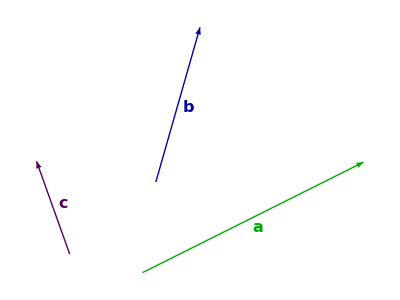

```mathematica
ClearAll[pthreevec]
pthreevec = Module[{v1,v2,v3,ox, oy},
v1 = e1 + 0.5e2;
v2 = 0.2 e1 + 0.7 e2;
v3 = (0.6)(-0.25 e1 + 0.7 e2);
ox = {0.3,0};
oy = {0, 0.2};

Graphics[ {
Thick
,Arrowheads[0.05]

,Green // Darker
,Arrow[{o,v1}]
,Text["a"//bold//fs, v1/2+0.05 rn[v1] ]

,Blue // Darker
,Arrow[{oy + 0.3v2,oy +(1+0.3)v2} ]
,Text["b"//bold//fs, oy+(1.6)v2/2+0.05 rn[v2]]

,Purple // Darker
,Arrow[{-ox + 0.2 v3,-ox +(1+0.2)v3} ]
,Text["c"//bold//fs, -ox +(1.4)v3/2+0.05 rn[v3]]

(*,Black,
PointSize[0.02],
Point[o],
Text["O" // fs, {-0.08,0}]*)
}]
]
```

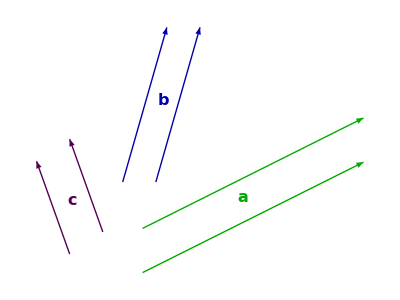

```mathematica
ClearAll[pthreevectx]
pthreevectx = Module[{v1,v2,v3,ox, oy},
v1 = e1 + 0.5e2;
v2 = 0.2 e1 + 0.7 e2;
v3 = (0.6)(-0.25 e1 + 0.7 e2);
ox = {0.3,0};
oy = {0, 0.2};

Graphics[ {
Thick
,Arrowheads[0.05]

,Green // Darker
,Arrow[{o,v1}]
,Arrow[{o + oy,v1 + oy}]
,Text["a"//bold//fs, v1/2-0.1 rn[v1] ]

,Blue // Darker
,Arrow[{oy + 0.3v2,oy +(1+0.3)v2} ]
,Arrow[{oy + 0.3v2 - ox/2,oy +(1+0.3)v2 - ox/2} ]
,Text["b"//bold//fs, oy+(1.6)v2/2-0.07 rn[v2]]

,Purple // Darker
,Arrow[{-ox + 0.2 v3,-ox +(1+0.2)v3} ]
,Arrow[{-ox/2 +oy/2 +  0.2 v3,-ox/2 +oy/2+(1+0.2)v3} ]
,Text["c"//bold//fs, -ox +(1.4)v3/2+0.09 rn[v3]]

(*,Black,
PointSize[0.02],
Point[o],
Text["O" // fs, {-0.08,0}]*)
}]
]
```

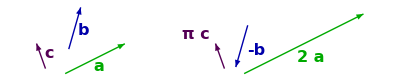

```mathematica
ClearAll[pthreevecscaled]
pthreevecscaled = Module[{v1,v2,v3,ox, oy, o2},
v1 = e1 + 0.5e2;
v2 = 0.2 e1 + 0.7 e2;
v3 = (0.6)(-0.25 e1 + 0.7 e2);
ox = {0.3,0};
oy = {0, 0.2};
o2 = {3,0};

Graphics[ {
Thick
,Arrowheads[0.03]

,Green // Darker
,Arrow[{o,v1}]
,Text["a"//bold//fs, v1/2+0.15 rn[v1] ]

,Green // Darker
,Arrow[{o2,o2+2v1}]
(*,Arrow[{o2,o2+v1}]*)
,Text["2 a"//bold//fs, o2 + 2v1/2+0.25 rn[v1] ]

,Blue // Darker
,Arrow[{oy + 0.3v2,oy +(1+0.3)v2} ]
,Text["b"//bold//fs, oy+(1.6)v2/2+0.15 rn[v2]]

,Blue // Darker
,Arrow[{o2 + 3oy + 0.3v2,o2 + 3oy + 0.3v2 - v2} ]
,Text["-b"//bold//fs, o2 + 3oy + 0.3v2 - v2/2+0.25 rn[v2]]

,Purple // Darker
,Arrow[{-ox + 0.2 v3,-ox +(1+0.2)v3} ]
,Text["c"//bold//fs, -ox +(1.4)v3/2+0.15 rn[v3]]

,Purple // Darker
(*,Arrow[{o2+-ox + 0.2 v3,o2+-ox +(Pi+0.2)v3} ]*)
,Arrow[{o2+-ox + 0.2 v3,o2+-ox +(1+0.2)v3} ]
,Text["π c"//bold//fs,o2 -ox +(Pi + 2*0.2)v3/2 - 0.25 rn[v3]]

(*,Black,
PointSize[0.02],
Point[o],
Text["O" // fs, {-0.08,0}]*)
}]
]
```

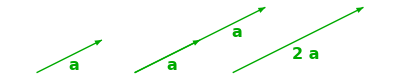

```mathematica
ClearAll[pvecplusvec]
pvecplusvec = Module[{v1,o2},
v1 = e1 + 0.5e2;
o2 = {3,0};

Graphics[ {
Thick
,Arrowheads[0.03]

,Green // Darker
,Arrow[{o,v1}]
,Text["a"//bold//fs, v1/2+0.15 rn[v1] ]

,Green // Darker
,Arrow[{o2/2,o2/2+2v1}]
,Arrow[{o2/2,o2/2+v1}]
,Text["a"//bold//fs, o2/2 +v1/2+0.15 rn[v1] ]
,Text["a"//bold//fs, o2/2 +3v1/2+0.15 rn[v1] ]

,Green // Darker
,Arrow[{o2,o2+2v1}]
(*,Arrow[{o2,o2+v1}]*)
,Text["2 a"//bold//fs, o2 + 2v1/2+0.25 rn[v1] ]
}]
]
```

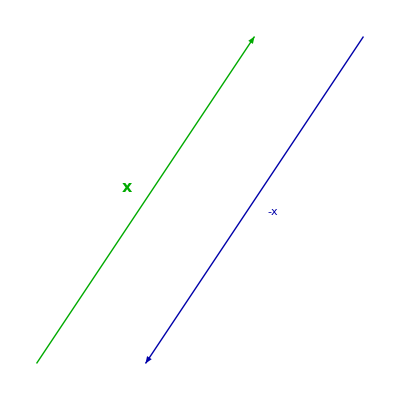

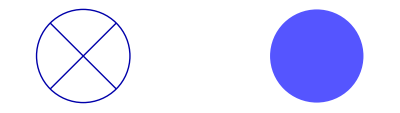

```mathematica
p1 = Module[{x0,x1,y0, y1},
x0 = o;
x1 = e1+1.5e2;
y0 = 1.5 e1+1.5e2;
y1 = e1/2;
Graphics[ {
Thick,
Arrowheads[0.05],
Green // Darker,
Arrow[{x0,x1}],
Text["x"//bold//fs,  (x0+x1)/2 + 0.1 rp[x1-x0]],
Blue // Darker,
Arrow[{y0, y1} ],
Text[Row[{"-"//fs,"x"//bold//fs}],  (y0+y1)/2 + 0.1 rp[y1-y0]]
}]
]



p3 = Module[{p1, p2,r},
r = 0.01;
p1 = r(e1+e2)/Sqrt[2];
p2 = r(e1-e2) /Sqrt[2];
Graphics[ {
Thick,
Blue//Darker,
Circle[o,r],

Line[{-p1, p1}],
Line[{-p2,p2}],
Blue// Lighter,
Disk[0.05 e1,r]
}]
]
```

```mathematica
peeters`exportForLatex["scalarOrientationFig1", p3]
```

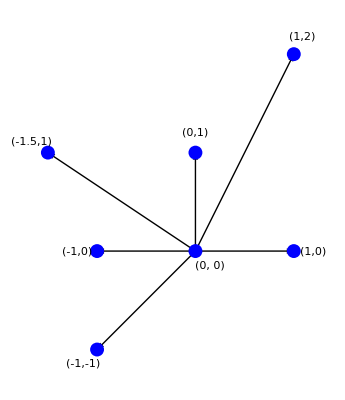

```mathematica
p5 = Module[{x},
x = {{1,0}, {1,2}, {0,1}, {-1.5,1},{-1,-1}, {-1,0}};
{ 
{
Thick,
Arrowheads[0.05]
}
,Arrow[{o,#}]&/@ x
, Text[Row[fs[#] &/@{"(", #[[1]], ",", #[[2]], ")"}],# + 0.2 Normalize[#]]&/@ x
,Blue
,PointSize -> 0.025
,Point[#]&/@ x
,Point[o]
, Black
, Text[Row[fs[#] &/@{"(0, 0)"}],0.15{1,-1}]
} // Flatten // Graphics

]
```

```mathematica
peeters`exportForLatex["coordinateRepresentationFig1", p5]
```

{coordinateRepresentationFig1.eps,coordinateRepresentationFig1pn.png}

```mathematica
(*peeters`exportForLatex["twiceVectorFig1", pvecplusvec]
peeters`exportForLatex["threeVectorsTxFig1", pthreevectx] 
peeters`exportForLatex["threeVectorsScaledFig1", pthreevecscaled] 
peeters`exportForLatex["threeVectorsFig1", pthreevec] 
peeters`exportForLatex["vectorAdditionFig1", psumoftwo]
peeters`exportForLatex["vectorSubtractionFig1", pdiffoftwo]
 *)
(*peeters`exportForLatex["vectorAdditionFig1", psumofthree]
peeters`exportForLatex["bw/vectorAdditionFig1", psumofthreebw]
peeters`exportForLatex["bw/VectorsWithOppositeOrientationFig1", pscalingbw] 
peeters`exportForLatex["color/VectorsWithOppositeOrientationFig1", pscaling] 
*)
```

{vectorAdditionFig1.eps,vectorAdditionFig1pn.png}

{bw/vectorAdditionFig1.eps,bw/vectorAdditionFig1pn.png}